# ITL sensor on Shipping Jig - Flatness only (No REF, so no AbsZ)

PZ Takacs

## ITL_onShippingJig_Flat.nb

## Extracted from SurfAnal10b

Version notes

2016.02.20 - Added higher order surface fitting to outlier cleanup section.
2015.09.30 - v04. Added CleanNotebookInOut functions to reset everything at start of next file for analysis. Removed EdgeScan from title.
2015.08.19 - Added Report TXT file ouput.Added CleanSlate to reset system during Init.
2015.08.17 - Rename to indicate this produces results for both AbsZ and Flatness from measurements made with sensor on MF01b fixture, rather than on shipping jig. Automatic export of all data products. Requires the datum origin to be at the CDD LL corner.
2015.06.22 - Modify for ITL sensor on MF01b for abs hgt and flatness. Edge scan does not enter into this analysis.
2014.11.21 - ver. 4 Customize for production CCD flatness and height measurement. Include upstemcal offset factor for absolute height correction.

## 1.0 Initialize - run this first to clear everything for new data input.

```mathematica
(*  ************CleanNotebookInOut**********************)
ClearAll[CleanNotebookInOut];

CleanNotebookInOut::usage="CleanNotebookInOut[] removes
the In and Out CellLabels from the notebook in which it is
evaluated and resets the line number to 1.  If the
RemoveOutput option is set to True then all Output cells in
the notebook are deleted as well.";

Options[CleanNotebookInOut]={RemoveOutput->False};
```

```mathematica
CleanNotebookInOut[opts___?OptionQ]:=Module[{nb,theNotebook,revisedNotebook,removeOutput},removeOutput=RemoveOutput/.Flatten[{opts,Options[CleanNotebookInOut]}];
$Line=0;
nb=SelectedNotebook[];
theNotebook=NotebookGet[nb];
revisedNotebook=theNotebook/.Cell[x___,CellLabel->_,y___]:>Cell[x,y];
NotebookPut[revisedNotebook,nb];
If[removeOutput,FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]];]
```

```mathematica
CleanNotebookInOut[RemoveOutput->True]
```

```mathematica
?CleanNotebookInOut
```

## 2.0 Initialize - execute AFTER 1.0

Select one of these to allow or suppress automatic output file generation.

```mathematica
autoOutput=True;
autoOutput=Input["Set autoOutput flag to False to suppress automatic uotput of data product files.",autoOutput]
```

True

Data and time of last saved modification. This is an Initialization cell that executes automatically whenever the nb is opened.

```mathematica
nb=EvaluationNotebook[]
```

m7hzs_shm13FrontEndObject[LinkObject["m7hzs_shm", 3, 1]]13ITL_onShippingJig_Flat_v04.nb/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Analysis codes/Production codes/ITL_onShippingJig_Flat_v04.nb

```mathematica
DateString["FileModificationTime"/.NotebookInformation[],TimeZone->0]
```

Tue 29 Mar 2016 20:20:00

```mathematica
Off[General::"spell1"]
(*<<"BarCharts`";<<"Histograms`";<<"PieCharts`"
<<"LinearRegression`"*)
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
$SystemID
```

MacOSX-x86-64

```mathematica
$OperatingSystem
```

MacOSX

#### Conversion factors to meters for numbers in the indicated units:

```mathematica
mm=10.^-3;
micron=10.^-6;
µm=10.^-6;
nm=10.^-9;
Angstroms=10.^-10;
micronsToAngstroms=10^4;
```

```mathematica
autoOutput
```

## 3.0 Full automated run starts here. Just answer the questions and the nb will run to completion and output all of the data products to the woring directory.

#### Execute following after setting the proper file path.

```mathematica
filepathfull
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/ITL prod sensors/ITL-007/MET-04 data/ITL-3800C-007_Flat_20160620-10H24M_run1.DAT

```mathematica
filepathfull=Input["Do Insert->FilePath and navigate to desired data file and select to enter here.",filepathfull]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/ITL prod sensors/ITL-007/MET-04 data/ITL-3800C-007_Flat_20160620-10H24M_run1.DAT

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/ITL prod sensors/ITL-007/MET-04 data

Use the filename form appropriate for the computer platform, either MacOSX or Windows

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
If[$OperatingSystem=="Windows",sep$="\\",sep$="/"];
```

```mathematica
manualcalcFlag=False; (*set for automated analysis*)
```

```mathematica
(*manualcalcFlag=True;*) (*to stop automated analysis with default parameters*)
```

### Enter upstemcal offset value here, for later correction of CCD absolute height relative to REF plane.

```mathematica
upstemcal=0.0;
```

```mathematica
upstemcal=Input["Enter upstemcal offset factor here. Default = 0",upstemcal]
```

0.

### Read in OGP txt format. Contours. This is treated as FREEFORM data, i.e. no set nrows or ncols.

Data is in the form of a big list of triplets in units of mm. The X,Y coordinate is included with the z-value. Note that this is NOT a rectangular data array, so can't use the array plot functions unless the data is padded to make a grid, which is not possible with OGP freefom data.

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/ITL prod sensors/ITL-007/MET-04 data

```mathematica
datain=.;datain2=.;datainXYZSR=.;skipnum=.;nRows=.;nCols=.;delx=.; dely=.;(*nominal scan values *)
```

```mathematica
fnames=FileNames["*.DAT"];Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | ITL-3800C-007_Flat_20160620-10H24M_run1.DAT
2 | ITL-3800C-007_Flat_20160620-10H24M_run2.DAT
3 | ITL-3800C-007_Flat_20160620-10H24M_run3.DAT

#### Pick the OGP file from the list

```mathematica
inst$="OGP"
```

OGP

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
nf=Input[TemplateApply[StringTemplate["Enter index of desired file in the list (0=Abort):\n<*Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm*>"]],nf]
```

3

```mathematica
If[nf<1,MessageDialog["Incorrect file number. Abort the run, please."];Interrupt[];Abort[]]
```

```mathematica
fileinfull =fnames[[nf]]
fileinroot=FileBaseName[fileinfull]
fileinS=fileinroot;
```

ITL-3800C-007_Flat_20160620-10H24M_run3.DAT

ITL-3800C-007_Flat_20160620-10H24M_run3

There is no separate REF file, so set filein to fileinS

```mathematica
fileinS=fileinroot<>"_FLAT_CCD_"
```

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD_

```mathematica
filein=fileinS;datain=Import[fileinfull,"Data"];
```

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
If[manualcalcFlag,Interrupt[] ](* Stop here to execute next expressons individually as needed to clean up data *)
```

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
workdir=filein<>"_files"
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/ITL prod sensors/ITL-007/MET-04 data

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD__files

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

New work dir created

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/_Production DATA/ITL prod sensors/ITL-007/MET-04 data/ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD__files

```mathematica
SelectionMove[nb,Next,Cell]
```

Strip out all of the Contour record, nulls and EORs, making one long list of points.

```mathematica
Length[datain]
Count[datain,{}] (* Counts the number of blank records in the file*)
```

1798

41

Replace this with new contour finder

```mathematica
datain2=Select[datain,Length[#]>0&];(*Strip out the blank lines*)
```

```mathematica
contourPos=Position[datain2,"Contour",2]
Length[contourPos]
```

{{2,1},{45,1},{88,1},{131,1},{174,1},{217,1},{260,1},{303,1},{346,1},{389,1},{432,1},{475,1},{518,1},{561,1},{604,1},{647,1},{690,1},{733,1},{776,1},{819,1},{862,1},{905,1},{948,1},{991,1},{1034,1},{1077,1},{1120,1},{1163,1},{1206,1},{1249,1},{1292,1},{1335,1},{1378,1},{1421,1},{1464,1},{1507,1},{1550,1},{1593,1},{1628,1},{1671,1},{1714,1}}

41

```mathematica
Length[datain2]
datain2=Select[datain2,NumericQ[#[[1]]]&]; (* Strip out all the lines that don't start with a number *)
Length[datain2]
```

1757

1714

```mathematica
datain2[[1;;10]]//TableForm;
```

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
If[manualcalcFlag,Interrupt[] ]
```

```mathematica
Manipulate[datain2[[i]],{i,1,Length[datain2],1}]
```

Strip out all but the Contour points

```mathematica
Length[datain]
```

1798

```mathematica
Dimensions[datain]
```

{1798}

```mathematica
datain[[1;;10]]
```

{{C:\Production_DATA\ITL-3800C-007\Flatness\20160620-10H24M\ITL_Flatness_run2.RTN,06/20/2016,11:17:01,3},{Contour,9,Start,good,scans},{0.492495,0.513545,-0.02005,mm},{1.44466,0.514564,-0.019834,mm},{2.53082,0.515697,-0.017332,mm},{3.58628,0.516673,-0.015527,mm},{4.43665,0.517216,-0.014118,mm},{5.37062,0.517691,-0.012323,mm},{6.42068,0.51755,-0.010377,mm},{7.54114,0.51802,-0.008094,mm}}

```mathematica
datain[[-10;;-1]]
```

{{34.5565,40.5137,0.052794,mm},{35.6279,40.5138,0.054389,mm},{36.5848,40.5136,0.05575,mm},{37.4717,40.5131,0.057772,mm},{38.6048,40.5137,0.060816,mm},{39.2376,40.5134,0.063046,mm},{40.4553,40.5136,0.066784,mm},{40.9386,40.5134,0.067726,mm},{},{EOR}}

```mathematica
Length[datain]
```

1798

Find all lines with less than 2 numbers and at least 1 string. This excludes all the the triplet lines with mm at the end.

```mathematica
charpos=Reap[Do[
If[(Count[datain[[i]],_?NumberQ]<2&&Count[datain[[i]],_?StringQ]>=1),Sow[{i,1}]],{i,Length[datain]}]];
```

```mathematica
charpos[[2,1]]//Length
```

43

```mathematica
Drop[charpos,1];
```

```mathematica
charpos2=Flatten[Drop[charpos,1],2]
```

{{1,1},{2,1},{46,1},{90,1},{134,1},{178,1},{222,1},{266,1},{310,1},{354,1},{398,1},{442,1},{486,1},{530,1},{574,1},{618,1},{662,1},{706,1},{750,1},{794,1},{838,1},{882,1},{926,1},{970,1},{1014,1},{1058,1},{1102,1},{1146,1},{1190,1},{1234,1},{1278,1},{1322,1},{1366,1},{1410,1},{1454,1},{1498,1},{1542,1},{1586,1},{1630,1},{1666,1},{1710,1},{1754,1},{1798,1}}

```mathematica
charpos3=Map[Part[#,1]&,charpos2,1]
```

{1,2,46,90,134,178,222,266,310,354,398,442,486,530,574,618,662,706,750,794,838,882,926,970,1014,1058,1102,1146,1190,1234,1278,1322,1366,1410,1454,1498,1542,1586,1630,1666,1710,1754,1798}

```mathematica
(*Find all the record numbers where Contour occurs*)cpos=Position[Extract[datain,charpos2],"Contour"]
```

{{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42}}

```mathematica
cpos+1  (*Add 1 to specify the record following the Contour record*)
```

{{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43}}

```mathematica
rifflvec=Riffle[cpos,cpos+1] (*Combine the 2 vectors*)
```

{{2},{3},{3},{4},{4},{5},{5},{6},{6},{7},{7},{8},{8},{9},{9},{10},{10},{11},{11},{12},{12},{13},{13},{14},{14},{15},{15},{16},{16},{17},{17},{18},{18},{19},{19},{20},{20},{21},{21},{22},{22},{23},{23},{24},{24},{25},{25},{26},{26},{27},{27},{28},{28},{29},{29},{30},{30},{31},{31},{32},{32},{33},{33},{34},{34},{35},{35},{36},{36},{37},{37},{38},{38},{39},{39},{40},{40},{41},{41},{42},{42},{43}}

```mathematica
(*Now pull out the index locations from charpos2 pointed to by the riffled vector*)
```

```mathematica
cpairs=Extract[charpos2,rifflvec]//Map[Part[#,1]&,#,1]&//Partition[#,2]&
```

{{2,46},{46,90},{90,134},{134,178},{178,222},{222,266},{266,310},{310,354},{354,398},{398,442},{442,486},{486,530},{530,574},{574,618},{618,662},{662,706},{706,750},{750,794},{794,838},{838,882},{882,926},{926,970},{970,1014},{1014,1058},{1058,1102},{1102,1146},{1146,1190},{1190,1234},{1234,1278},{1278,1322},{1322,1366},{1366,1410},{1410,1454},{1454,1498},{1498,1542},{1542,1586},{1586,1630},{1630,1666},{1666,1710},{1710,1754},{1754,1798}}

Enter a specific list of desired regions as the iterator for the Do loop.

```mathematica
(*Now take the range of points from datain between the range pairs. Drop the first record in each range (Contour}*)
```

```mathematica
datain4=.;
```

```mathematica
datain4=Reap[
Do[Sow[Take[datain,{cpairs[[i,1]]+1,cpairs[[i,2]]-2}]],{i,Length[cpairs]}]
]//Drop[#,1]&//Flatten[#,3]&;
```

```mathematica
Length[datain4]
```

1714

```mathematica
datain2=datain4;
```

#### All data points are now in one continuous list. All the contours are merged together

#### continue here

```mathematica
datain3x=Take[datain2,All,3];(* Strip off the XYZ numbers*)
```

Convert z-vals to microns:

```mathematica
datain3x[[1]]
datain3x=Map[MapAt[Times[#,10^3]&,#,3]&,datain3x];
datain3x[[1]]
```

{0.492495,0.513545,-0.02005}

{0.492495,0.513545,-20.05}

```mathematica
xunit$="mm";yunit$="mm";zunit$="µm"; (*These are now current units*)
```

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
datainXYZS=datain3x;
datainXYZSR=datainXYZS; (* No REF. Copy surface into SR array. *)
```

```mathematica
skipnum=.;cloudXYZ=.
```

```mathematica
cloudXYZ=datainXYZSR;
Dimensions[cloudXYZ]
```

{1714,3}

Range of raw z-values:

```mathematica
{Min[cloudXYZ[[All,{3}]]],Max[cloudXYZ[[All,{3}]]]}
```

{-20.05,67.726}

### Plot free-form data list not on uniform grid

#### Start next range clean-up here. Keep eliminating points from cloudXYZ based on x and y and z range criteria.

Execute the appropriate unpacking expression and rearrange the cloudXYZ as necessary.
This depends on the ordering of the XYZ values in each triplet:  XYZ or ZYX

```mathematica
xvals=Take[cloudXYZ,All,{1}]//Flatten;
yvals=Take[cloudXYZ,All,{2}]//Flatten;
zvals=Take[cloudXYZ,All,{3}]//Flatten;
```

```mathematica
{xmin=Min[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],zmax=Max[zvals],Mean[zvals],StandardDeviation[zvals]}//N
```

{0.491992,40.9415}

{0.513305,40.519}

{-20.05,67.726,23.0714,19.6183}

```mathematica
{deltaX=xmax-xmin, deltaY=ymax-ymin,deltaZ=zmax-zmin}
```

{40.4495,40.0057,87.776}

```mathematica
rowscols$="cloud" (*"sparse"*)
```

cloud

Next expression may not contain desired array on first pass. Why???? BEWARE

```mathematica
vp={0,-2,2};
Dynamic[vp];
```

```mathematica
Dimensions[cloudXYZ]
```

{1714,3}

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
lpp01=ListPointPlot3D[cloudXYZ,PlotRange->All,ViewPoint->vp,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->9],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw data"]
```

-Graphics3D-

```mathematica
If[autoOutput,Export[ToString[StringDrop[fileinS,0]]<>"_CCDraw.tiff",lpp01,"ImageEncoding"->"LZW",ImageResolution->100]]
```

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD__CCDraw.tiff

```mathematica
Button["Export raw data SUT plot",Export[fileinS<>"SUTraw.tiff",lpp01,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export raw data SUT plot

#### Find the SUT. There is no REF for flatness

```mathematica
xyPCSrange={{xmin,xmax},{ymin,ymax}}  (*Use actual data range *)
```

{{0.491992,40.9415},{0.513305,40.519}}

First discard the points in the MCS that are measured before the datum origin defining the PCS is set on the hole center.

```mathematica
{{xminPCS,xmaxPCS},{yminPCS,ymaxPCS}}=xyPCSrange
```

{{0.491992,40.9415},{0.513305,40.519}}

```mathematica
testRegion =Reap[ Do[If[
cloudXYZ[[i]][[1]]<xmaxPCS&& cloudXYZ[[i]][[1]]>xminPCS&&
cloudXYZ[[i]][[2]]<ymaxPCS&& cloudXYZ[[i]][[2]]>yminPCS
,Sow[cloudXYZ[[i]]]],{i,Length[cloudXYZ]}]];
PCSregion=Drop[testRegion,1]//Flatten[#,2]&;
Length[PCSregion]
```

1710

Verify that the proper region has been selected.

```mathematica
PCSregionplt=ListPointPlot3D[PCSregion,PlotRange->All,ViewPoint->{0,0,Infinity},ColorFunction->"Rainbow",ImageSize->200,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nPCSregion"]
```

-Graphics3D-

Note: There is no REF data points for ITL Flatness only data files. Ignore the error message.

```mathematica
SUTdata=PCSregion;
```

```mathematica
splt=ListPointPlot3D[SUTdata,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->200,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw SUT region"]
```

-Graphics3D-

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
SUTdatatrim=SUTdata;
```

## Now work on Flatness of SUT. Trim outliers by fitting high order surface first and removing outliers. Then iterate once more with pure plane fit.

#### Clean up SUT points, removing outliers. MUST EXECUTE THIS SECTION.

```mathematica
fitnumflag=Input["Enter num for fit to apply. If finished with trim, enter 1 (pure plane).\n0 = piston only\n1 = pure plane\n2 = pure sphere\n3 = general {m,n}order polynomial\n4 = Chebyshev polynomial (m,n)" ]
```

1

Don’t output data when points are being trimmed, only when plane fit is selected.

```mathematica
If[fitnumflag==1,autoOutput=True,autoOutput=False]
```

True

#### COntinue after fit selection

Do the fit here. The working array is worksurf. Make sure it has the desired data in it.

Need to normalize the x and y values when doing the Chebyshev fit, using the actual values for xlen and ylen. For the other cases, use xlen=ylen=1 in the normaization expression.

```mathematica
xlen=1;ylen=1;
```

```mathematica
Switch[fitnumflag,
0,(*Piston only*)fitbasis={1};fitidxS$="0";fitidxS$="0";Print["Piston only fit"],
1, (*Pure Plane*)fitbasis={1,x,y};fitidxS$="S1,1"(*fitord$=StringTake[TS[fitbasis],{2,-2}]*),
2,(*Pure Sphere*)fitbasis={1,x,y,x y,x^2+y^2};fitidxS$="Ssph"(*fitord$=StringTake[TS[fitbasis//InputForm],{2,-2}]*),
3,(*General cartesian polynomial*)fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
fitidxS$="S"<>fitidxS$;
(*fitord$=StringTake[TS[sp],{2,-2}];*)
fitbasis={};
Do[
If[i+j>ordx+ordy,Null,AppendTo[fitbasis,x^i y^j]],{i,0,ordx},{j,ordy,0,-1}],
4,(*Chebychev poly*)fitidxS$=InputString["Enter x and y order numbers of 2D surface fit desired, separated by a comma, i.e. 1,2"];
sp=StringSplit[fitidxS$,","]//ToExpression;
ordx=sp[[1]];ordy=sp[[2]];
fitidxS$="S"<>"Chb"<>fitidxS$;
(*fitord$=StringTake[TS[sp],{2,-2}];*)
(*compute the required xlen and ylen for this case*)
xlen=xmax-xmin//N;ylen=ymax-ymin//N;
fitbasis={};
xs[x_,xmax_,xmin_]:=2/(xmax-xmin) (x-xmin-(xmax-xmin)/2);
fitbasis=Table[HoldForm[ChebyshevT[ii,xs[x,xmax,xmin]]] HoldForm[ChebyshevT[jj,xs[y,ymax,ymin]]]/.ii->i/.jj->j,{i,0,ordx},{j,0,ordy}]//Flatten;
]
```

S1,1

```mathematica
SUTfit[x_,y_]=Fit[SUTdatatrim,fitbasis,{x,y}]
```

-19.7702+1.54122 x+0.518848 y

```mathematica
vp1={2,0,.5};
```

```mathematica
sutfitplt=Plot3D[SUTfit[x,y],{x,xmin,xmax},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]];
```

```mathematica
SUTandFITplane=Show[splt,sutfitplt,PlotRange->All,ViewPoint->Dynamic[vp1],PlotLabel->fileinS<>"\nPlane fit to trimmed SUT points"]
```

-Graphics3D-

```mathematica
Dynamic[vp1]
```

Now trim outliers more than some value away fom the fit plane value.
First subtract plane fit to the full SUT data. NEW VERSION for flatnees stats

```mathematica
SUTresids=Table[{SUTdatatrim[[i,1]],SUTdatatrim[[i,2]],SUTdatatrim[[i,3]]-SUTfit[SUTdatatrim[[i,1]],SUTdatatrim[[i,2]]]},{i,Length[SUTdatatrim]}];
Length[SUTresids]
```

1710

```mathematica
ListPointPlot3D[SUTresids,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw SUT region"]
```

-Graphics3D-

```mathematica
SUTresidsZ=SUTresids[[All,{3}]]//Flatten; (*extract the z-values*)
```

```mathematica
{Mean[SUTresidsZ],Median[SUTresidsZ],StandardDeviation[SUTresidsZ]}
```

{3.88638×10^-14,-0.141471,1.47988}

```mathematica
{Min[SUTresidsZ],Max[SUTresidsZ]}
```

{-3.67169,12.9017}

```mathematica
{Quantile[SUTresidsZ,0.005],Quantile[SUTresidsZ,.995]}
```

{-2.44696,9.22116}

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
sutflathist0=Histogram[SUTresidsZ,40,PlotRange->All,ImageSize->300];(*These are the residuals after removing plane fit*)
```

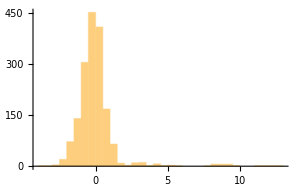

```mathematica
sutflathist01={sutflathist0,Dynamic[MousePosition["Graphics"]]}
```

Trim the outliers here.

```mathematica
{threshmin,threshmax}={Quantile[SUTresidsZ,0.0],Quantile[SUTresidsZ,1.0]}
```

{-3.67169,12.9017}

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
{threshmin,threshmax}=Input[{sutflathist01,"Enter {min,max} threshold values for trimming bad points."},{threshmin,threshmax}]
```

{-3.67169,6}

Trim both the XYZ and the Z data lists

```mathematica
SUTresidsZtrim=
Drop[
Reap[ 
Do[
If[
SUTdatatrim[[i,3]]-SUTfit[SUTdatatrim[[i,1]],SUTdatatrim[[i,2]]]<threshmax && SUTdatatrim[[i,3]]-SUTfit[SUTdatatrim[[i,1]],SUTdatatrim[[i,2]]]>threshmin,
Sow[SUTdatatrim[[i,3]]-SUTfit[SUTdatatrim[[i,1]],SUTdatatrim[[i,2]] ]]
],
{i,Length[SUTdatatrim]}
]
],
1]//Flatten[#,2]&;
```

```mathematica
SUTresidsZtrim[[1;;10]]
```

{-1.30532,-2.55734,-1.72994,-1.55215,-1.45405,-1.09875,-0.77106,-0.215186,-0.231974,-0.561522}

```mathematica
SUTdatatrim2=
Drop[
Reap[
 Do[
If[
SUTdatatrim[[i,3]]-SUTfit[SUTdatatrim[[i,1]],SUTdatatrim[[i,2]]]<threshmax && SUTdatatrim[[i,3]]-SUTfit[SUTdatatrim[[i,1]],SUTdatatrim[[i,2]]]>threshmin,Sow[SUTdatatrim[[i]]]
],
{i,Length[SUTdatatrim]}]
],
1]//Flatten[#,2]&;
```

```mathematica
SUTdatatrim=SUTdatatrim2;
```

```mathematica
SUTresidsXYZtrim=Table[{SUTdatatrim[[i,1]],SUTdatatrim[[i,2]],SUTresidsZtrim[[i]]},{i,Length[SUTdatatrim]}];
```

```mathematica
rmstrim=StandardDeviation[SUTresidsZtrim]
```

0.93741

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
ListPointPlot3D[SUTresidsXYZtrim,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nRMS= "<>ToString[rmstrim]<>", raw SUT region"]
```

-Graphics3D-

Loop up to adjust fit for better outlier trim

```mathematica
moretrim=Input["Enter 1 to loop up for more trim or for final pass for plane fit; 0 for good to go",moretrim]
```

0

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
If[moretrim==1, NotebookLocate["fit for trim"],SelectionMove[nb,Next,Cell]]
```

### Use these SUT zresids for Flatness statistics. This excludes tilt effects and only looks at intrinsic surface flatness.

```mathematica
sutlen$=ToString[Length[SUTdatatrim]]
```

1684

```mathematica
maxzF=Max[SUTresidsZtrim];minzF=Min[SUTresidsZtrim];sigmaF=StandardDeviation[SUTresidsZtrim];
zbinF=BinCounts[SUTresidsZtrim,(maxzF-minzF)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrangeF95=hrange[SUTresidsZtrim,0.025,0.975];
PVrangeF95=hgtrangeF95[[2]]-hgtrangeF95[[1]];
hgtrangeF99=hrange[SUTresidsZtrim,0.005,0.995];PVrangeF99=hgtrangeF99[[2]]-hgtrangeF99[[1]];
sigmaF//NumberForm[#,5]&;
```

```mathematica
sutflatplt=ListPointPlot3D[SUTresidsXYZtrim,PlotRange->All,ViewPoint->Dynamic[vp1],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval","Z [µm]"},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->9],PlotLabel->fileinS<>": SUT flatness"<>"\n95%range="<>ToString[hgtrangeF95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeF95[[2]]-hgtrangeF95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeF99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeF99[[2]]-hgtrangeF99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sigmaF//NumberForm[#,3]&]<>zunit$]
```

-Graphics3D-

```mathematica
If[autoOutput,Export[fileinS<>"plot1.tiff",sutflatplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD_plot1.tiff

```mathematica
Button["Export SUT Flatness plot",Export[fileinS<>"plot1.tiff",sutflatplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export SUT Flatness plot

```mathematica
SelectionMove[nb,Next,Cell]
```

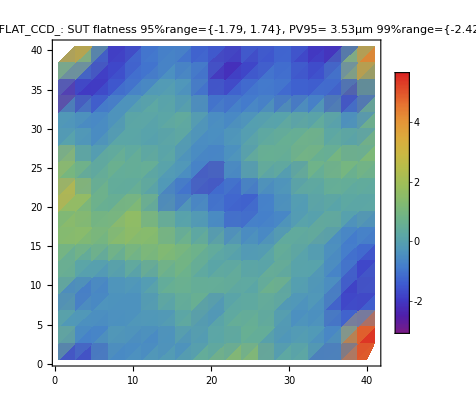

```mathematica
surfdenplt=ListDensityPlot[SUTresidsXYZtrim,InterpolationOrder->1,MaxPlotPoints->20,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{minzF,maxzF}},LabelStyle->Directive[Bold,FontFamily->"Helvetica"]],PlotLabel->fileinS<>": SUT flatness"<>"\n95%range="<>ToString[hgtrangeF95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeF95[[2]]-hgtrangeF95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeF99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeF99[[2]]-hgtrangeF99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sigmaF//NumberForm[#,3]&]<>zunit$,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->9]]
```

```mathematica
If[autoOutput,Export[fileinS<>"_surfdens.tiff",surfdenplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD__surfdens.tiff

```mathematica
Button["Export SUT surface density plot",Export[fileinS<>"_surfdens.tiff",surfdenplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export SUT surface density plot

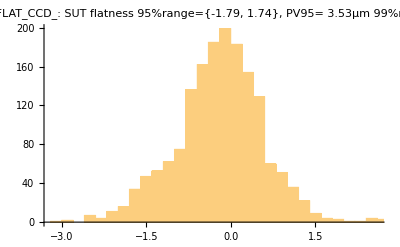

```mathematica
sutflathist=Histogram[SUTresidsZtrim,40,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->9],PlotLabel->fileinS<>": SUT flatness"<>"\n95%range="<>ToString[hgtrangeF95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeF95[[2]]-hgtrangeF95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeF99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeF99[[2]]-hgtrangeF99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sigmaF//NumberForm[#,3]&]<>zunit$](*These are the residuals after removing plane fit*)
```

```mathematica
If[autoOutput,Export[fileinS<>"histo.tiff",sutflathist,"ImageEncoding"->"LZW",ImageResolution->100]]
```

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD_histo.tiff

```mathematica
Button["Export SUT Flatness histogram",Export[fileinS<>"histo.tiff",sutflathist,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export SUT Flatness histogram

```mathematica
SelectionMove[nb,Next,Cell]
```

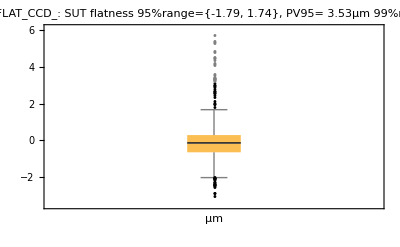

```mathematica
sbwcF=BoxWhiskerChart[SUTresidsZtrim,{"Outliers",{"MeanMarker",1.0,Thick}},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->9],PlotLabel->fileinS<>": SUT flatness"<>"\n95%range="<>ToString[hgtrangeF95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeF95[[2]]-hgtrangeF95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeF99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeF99[[2]]-hgtrangeF99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sigmaF//NumberForm[#,3]&]<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
If[autoOutput,Export[fileinS<>"bw.tiff",sbwcF,"ImageEncoding"->"LZW",ImageResolution->100]]
```

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD_bw.tiff

```mathematica
Button["Export Flatness whisker chart file",Export[fileinS<>"bw.tiff",sbwcF,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export Flatness whisker chart file

```mathematica
quantlist=Reverse[{0.0,0.005,0.01,0.025,0.25,0.50,0.75,0.975,0.99,0.995,1.0}];
```

```mathematica
qresF=Quantile[SUTresidsZtrim,quantlist];
```

```mathematica
qtableF=Transpose[{quantlist,qresF}];
%//TableForm
```

1. | 5.65357
0.995 | 4.39917
0.99 | 3.3303
0.975 | 1.73999
0.75 | 0.29081
0.5 | -0.148589
0.25 | -0.644247
0.025 | -1.78666
0.01 | -2.13688
0.005 | -2.42151
0. | -3.07771

```mathematica
If[autoOutput,Export[fileinS<>"quantile.xlsx",Prepend[qtableF,{fileinS<>", SUT flatness Quantiles"}],"XLSX"]]
```

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD_quantile.xlsx

```mathematica
Button["Export Flatness Quantile table file",Export[fileinS<>"quantile.xlsx",Prepend[qtableF,{fileinS<>", SUT flatness Quantiles"}],"XLSX"]]
```

Export Flatness Quantile table file

```mathematica
If[autoOutput,Export[fileinS<>"data.xlsx",Join[{{fileinS}},{{"Fit order = "<>fitidxS$}},SUTresidsXYZtrim],"XLSX"]]
```

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD_data.xlsx

```mathematica
Button["Export XYZ flatness height data.",Export[fileinS<>"data.xlsx",Join[{{fileinS}},{{"Fit order = "<>fitidxS$}},SUTresidsXYZtrim],"XLSX"]]
```

Export XYZ flatness height data.

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
strimplt=ListPointPlot3D[SUTresidsXYZtrim,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->9],PlotRange->All,ViewPoint->Dynamic[vp1],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>": SUT flatness"<>"\n95%range="<>ToString[hgtrangeF95//NumberForm[#,3]&]<>", PV95= "<>ToString[hgtrangeF95[[2]]-hgtrangeF95[[1]]//NumberForm[#,3]&]<>zunit$<>
"\n99%range="<>ToString[hgtrangeF99//NumberForm[#,3]&]<>", PV99= "<>ToString[hgtrangeF99[[2]]-hgtrangeF99[[1]]//NumberForm[#,3]&]<>zunit$<>
"\nsdev="<>ToString[sigmaF//NumberForm[#,3]&]<>zunit$]
```

-Graphics3D-

```mathematica
SelectionMove[nb,Next,Cell]
```

#### Generate report statistics .txt output file.

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
statreport=StringTemplate["Summary statistics for e2v sensor data file:\n\t `1`.\n\nFlatness (CCD-031)\n\tPV95% = `2`\t[<10µm to PASS]\n\tPV99% = `7`\n\nQuantiles\n`3`\n\nReport generated `4`\nNotebook version: `5`\nLast modified: `6`"

][fileinS,PVrangeF95,qtableF//TableForm,DateString[],CurrentValue["NotebookFileName"],"FileModificationTime"/.NotebookInformation[]//DateString,PVrangeF99]
```

Summary statistics for e2v sensor data file:
	 ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD_.

Flatness (CCD-031)
	PV95% = 3.52665	[<10µm to PASS]
	PV99% = 6.82068

Quantiles
1.    5.65357
0.995 4.39917
0.99  3.3303
0.975 1.73999
0.75  0.29081
0.5   -0.148589
0.25  -0.644247
0.025 -1.78666
0.01  -2.13688
0.005 -2.42151
0.    -3.07771

Report generated Mon 20 Jun 2016 14:21:33
Notebook version: ITL_onShippingJig_Flat_v04.nb
Last modified: Tue 29 Mar 2016 16:20:00

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
If[autoOutput,Export[fileinS<>"_CCD_stat_report.txt",statreport,"TEXT"]]
```

ITL-3800C-007_Flat_20160620-10H24M_run3_FLAT_CCD__CCD_stat_report.txt

```mathematica
Button["Export statistics TXT file.",Export[fileinS<>"_CCD_stat_report.txt",statreport,"TEXT"]]
```

Export statistics TXT file.

#### To iterate after this run, execute the following 2 cells.

```mathematica
SUTdata=SUTdatatrim;
```

```mathematica
NotebookLocate["SUTdata start"]
```

#### To read in a new data file, go to 1.0 and start over

```mathematica
NotebookLocate["New data Start over"]
```

## End of SUT flatness section.

## END of main analysis program.

## Remove obvious outliers from SUTdata if necessary. Skip this section if not necessary.

```mathematica
{minS,medianS,maxS,stddevS}=Operate[{Min[#],Median[#],Max[#],StandardDeviation[#]}&,SUTdata[[All,{3}]]//Flatten,0]
```

```mathematica
MedianDeviation[SUTdata[[All,{3}]]//Flatten]
```

```mathematica
threshS=3*(Min[maxS-medianS,medianS-minS])(*Set trim threshold to 3 times the smaller deviation from the median*)
```

```mathematica
threshS=3*stddevS(*Set trim threshold to 3 times the smaller deviation from the median*)
```

```mathematica
Length[SUTdata]
```

```mathematica
testS=.;
testS =Reap[ Do[If[
Abs[SUTdata[[i]][[3]]-medianS]<threshS
,Sow[SUTdata[[i]]]],{i,Length[SUTdata]}]];
testS=Drop[testS,1]//Flatten[#,2]&;
```

```mathematica
Length[testS]
```

```mathematica
If[Length[testS]==Length[SUTdata],MessageDialog["No points were trimmed from SUTdata"]]
```

```mathematica
If[Length[testS]>0,SUTdata=testS,MessageDialog["Problem with trimming SUTdata"]];(*Abort if problem trimming SUT data*)
```

```mathematica
testS=.;
```

```mathematica
splt=ListPointPlot3D[SUTdata,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nSUT-outliers"]
```

# Junk

## Define statistical functions for profile data.

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}]
```

MAKE SURE THE FOURIER OPTIONS ARE SET CORRECTLY EACH TIME THE FT IS DONE.

Define the biased stddev functiion. The built in StdDev fcn has n-1 in the denom. Change it to n.

Now compute std dev in different ways: The default StandardDeviation is the unbiased version, with n-1 in the denominator.

```mathematica
sdevBiased=.
```

```mathematica
sdevUnB[in_]:=N[StandardDeviation[in]]
```

```mathematica
sdevBiased[in_]:=StandardDeviation[in]Sqrt[(Length[in]-1)/Length[in]]
```

```mathematica
rmsBias[in_]:=Sqrt[Plus@@(in^2)/Length[in]]
```

Next is the RMS. Sum the squares, divide by N and then take the root. (Root of the Mean Square)

```mathematica
rmsrawbiased=.;
```

```mathematica
rms[in_]:=N[√((Plus@@((in)^2))/Length[in])]
```

See that one must subtract the mean from the input data first, before squaring, in order to compute the standard deviation correctly.

```mathematica
sdevBruteUnBiased[in_]:=N[√((Plus@@((in-Mean[in])^2))/(Length[in]-1))]
```

```mathematica
detrend[anylist_,order_Integer]:=Block[{npts,xlist,fitlist,x},
If[
order>=0,
xlist=Table[x^i,{i,0,order}];
		npts=Length[anylist];
		func=Fit[anylist,xlist,x];
		fitlist={};
		Do[AppendTo[fitlist,func],{x,1,npts}];
		Return[anylist-fitlist],
Return[anylist]
]
]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list.

```mathematica
psd1[in_,delx_]:=(SetOptions[Fourier,FourierParameters->{1,1}];
nPts=Length[in];
FTwork=Fourier[in];
psd2side=(2 delx/nPts) Abs[FTwork]^2;
psd1side=Drop[psd2side,-Floor[(nPts-1)/2]];
(*Apply bookkeeping factors to end terms*)
psd1side[[1]]=psd1side[[1]]/2; 
If[EvenQ[nPts],psd1side[[-1]]=psd1side[[-1]]/2,Null];
psd1side
)
```

```mathematica
npts=.
```

```mathematica
test11={1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
psd1[test11,1.]
```

```mathematica
nPts
```

```mathematica
Length[psd2side]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list. NOTE: Need to know the length of the input z-vector for the ntot number. Can't get it from the length of the psd list. It should be the length of the psd2side list if this corresponds to the input psd list.

```mathematica
rmspsdIDX[psd_,nztot_,delx_,lo_,hi_]:=(rmsval=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];Print["RMS over index range [",lo,",",hi,"] = ",rmsval])
```

```mathematica
rmspsd[psd_,nztot_,delx_,lo_,hi_]:=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];
```

Now generalize the variance calculation to apply to zero-padded data to give the same result as for the original data set. Need to boost up each term separately.

```mathematica
varGen[anylist_,beforeLen_,afterLen_]:=N[sfac=afterLen/beforeLen;(sfac Plus@@(anylist^2))/afterLen-sfac^2 ((Plus@@anylist)/afterLen)^2]
```

```mathematica
sdevGen=√varGen[worklist,nbefore,nafter]
```

#### Add a point digitizer to a plot. Results are put into vector "res".

```mathematica
locatePts[plotname_]:=
Block[ {}, 
res = {}; 
Dynamic[res]; 
  EventHandler[ 
         plotname, {"MouseDown" :>( AppendTo[res, MousePosition["Graphics"]])} 
        ] ]
```

#### The following tick function rescales the axes labels from the default [xmin, xmax] range by offsetting the starting point by b and scaling the tick value by m. Note that you need to specify the AxesOrigin in terms of the unshifted function.

```mathematica
$TextStyle={FontFamily->Arial,FontSize->10}
```

```mathematica
Style[PlotLabel,DefaultOptions->{FontFamily->Arial}]
```

```mathematica
tickf[min_,max_,m_,b_,step_]:= Table[{i,m (i-b)},{i,min,max,step}]
```

File name conventions

```mathematica
filename=.;filenamefull=.;fnames=.;plotname=.;filepath=.;filepathfull=.;
```

```mathematica
filein=.;fileinroot=.;fileinS=.;
```

Isolate the CCD region. THis will define the inclusion limits in Y-dir for dividing the data into REF and SUT regions.

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
If[manualcalcFlag,Input["Abort and set sliders now to isolate CCD surface region, then execute next section."],Input["Auto calc sets SUT range automatically"]]
```

#### Fix the xyrange to isolate the SUT region from the REF surfaces. Requires the datum origin to be at the CDD LL corner.

```mathematica
xyrange={{0.,45.},{0.,45.}}
```

```mathematica
{{xminCCD,xmaxCCD},{yminCCD,ymaxCCD}}=xyrange
```

```mathematica
{{imin,imax},{jmin,jmax}}=.;
```

```mathematica
{{xminCCD,xmaxCCD},{yminCCD,ymaxCCD}}//TableForm
```

```mathematica
SelectionMove[nb,Next,Cell]
```

```mathematica
testS=.;testR=.;SUTdata=.;REFdata=.;
```

```mathematica
testS =Reap[
 Do[
If[
PCSregion[[i]][[1]]<xmaxCCD&& PCSregion[[i]][[1]]>xminCCD&&
PCSregion[[i]][[2]]<ymaxCCD&& PCSregion[[i]][[2]]>yminCCD
,Sow[PCSregion[[i]],x]
,Sow[PCSregion[[i]],y]
],{i,Length[PCSregion]}
]
];
SUTdata=testS[[2,1]];
REFdata = testS[[2,2]];
{Length[SUTdata],Length[REFdata]}
tests=.;
```

#### Execute the locate statement to jump back up to the beginning.

```mathematica
NotebookLocate["New data Start over"]
```